```mathematica
Clear["Global`*"]
```

```mathematica
(*For prolate:*)
Le=Log[(1+e)/(1-e)];
XaP=8/3 e^3(-2e+(1+e^2)Le)^-1;
YaP=16/3 e^3(2e+(3 e^2-1)Le)^-1;
```

```mathematica
Limit[XaP,e->0]
```

1

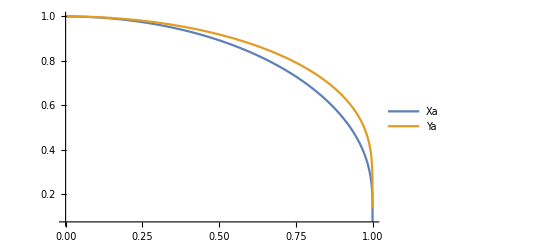

```mathematica
Plot[Evaluate[{XaP,YaP}/.{e->ee}],{ee,0.0001,1},PlotLegends->{"Xa","Ya"}]
```

```mathematica
e=0.7;
b=1 √(1-e^2);
N[b,14]
```

0.714143

```mathematica
vT[d_]:=-{0,1,0}.((d⊗d)/XaP+(IdentityMatrix[3]-d⊗d)/YaP);
```

```mathematica
vT[{1/(√2),1/(√2),0}]
```

{-0.0420505,-1.25302,0.}

```mathematica
(*For ellipsoids:
Fx=-(16πμabc)/(χ0+α0a^2) U; and similar for other directions
*)
a=1;
b=√(1-e1^2);
c=√(1-e2^2);
Δ[t_,e11_,e22_]:=√((a^2+t)(b^2+t)(c^2+t))/.{e1->e11,e2->e22};
α0[q_,e11_,e22_]:=a b c NIntegrate[1/((q^2+t) Δ[t,e11,e22]),{t,0,Infinity}]/.{e1->e11,e2->e22};
χ0[q_,e11_,e22_]:=a b c NIntegrate[1/Δ[t,e11,e22],{t,0,Infinity}]/.{e1->e11,e2->e22};
```

```mathematica
χ0[a,0.8,0.5]
```

1.26936

```mathematica
R[q_,e11_,e22_]:=16/6(b c)/(χ0[q,e11,e22]+α0[q,e11,e22] q^2)/.{e1->e11,e2->e22};
```

```mathematica
R[a,0.8,0.8]
XaP/.e->0.8
R[b/.e1->0.8,0.8,0.8]
YaP/.e->0.8
```

0.681492

0.681492

0.754026

0.754026